## The Mathematica Code by Dr. Alessandro Limongiello (alessandro.limongiello@unina.it) The following Mathematica code is associated to the Paper "On the mechanisms underlying the depolarization block in the spiking dynamics of CA1 pyramidal neurons" (D. Bianchi, A. Marasco, A.Limongiell ,C. Marchetti, H. Marie, B. Tirozzi, M. Migliore, 2012, J. Comput. Neurosci. ), and refers to the bifurcation analysis of the somatic model. We remark that these lines of code are extracted by an original package that perform the stability and biforcation analyses of a general somatic model. Eigenvalues Calculation

```mathematica
CalcoloEqEigenBio[deltaV_] :=
   Module[{},
   

      i0 = i1;
	  conc0 = conc1;
	  v0 = v1 + deltaV;
	  sol = FindRoot[(eqE[[17]]/.{varEqList[[1]]->v0,varEqList[[17]]->concPar})==0,{concPar,conc0}];
	  v2=v0;

	  conc2=sol[[1,2]];
	  
	  sol2=FindRoot[Evaluate[(eqE[[1]]/.{varEqList[[1]]->v2,varEqList[[17]]->conc2,Iext->curr})]==0,{curr,i1}];
	  i2 = sol2[[1,2]];

	  dimSys = Length[sys1];

	  var1List = Table[varEqList[[mm]]->(eqE[[mm]]/. {varEqList[[17]]->conc2, varEqList[[1]] -> v2}),{mm,2,dimSys-1}];
	  var1List = Append[var1List,varEqList[[1]] -> v2];
	  var1List = Append[var1List,Iext -> i2];
	  var1List = Append[var1List,varEqList[[17]]->conc2];

	  eigenSingle = Eigenvalues[Jacob //. var1List];   
      ntot = Length[eigenSingle];
	  Rneg = Length[Select[eigenSingle, Element[#, Reals] && # < 0 && Abs[#] > zero &]];
      Rzero = Length[Select[eigenSingle, Element[#, Reals] && Abs[#] < zero &]];
      Rpos = Length[Select[eigenSingle, Element[#, Reals] && # > 0 && Abs[#] > zero &]];
	  Cneg = Length[Select[eigenSingle, Im[#] != 0 && Re[#] < 0 && Abs[Re[#]] > zero &]];
      Czero = Length[Select[eigenSingle, Im[#] != 0 && Abs[Re[#]] < zero &]];
      Cpos = Length[Select[eigenSingle, Im[#] != 0 && Re[#] > 0 && Abs[Re[#]] > zero &]];



      eqCod = Which[
            Rzero + Czero + Cpos + Rpos == 0 && Cneg > 0, 1,
            Rzero + Cpos + Rpos == 0 && Czero > 0, 2,
            (Rzero + Czero == 0) && (Cpos + Cneg)>0 && Cpos + Rpos > 0, 3,
            Rzero + Czero + Cpos + Rpos + Cneg == 0 && Rneg > 0, 4,
            Rzero + Czero + Cpos + Cneg == 0 && Rpos > 0 (*&& Rneg > 0*), 5,
            Rpos + Czero + Cpos + Cneg == 0 && Rzero > 0 (*&& Rneg > 0*), 6,
			(*Cpos + Rpos == 0 && Czero > 0, 7*)
			(*Rzero + Czero == 0 && Rpos == ntot, 7*)
			Cpos + Rpos == 0 && Rzero + Czero > 0,7
            ];


 
	  eigenList[eqCod] = Append[eigenList[eqCod], eigenSingle];
      pSol[1] = Append[pSol[1], {(i2/currConvFatt), v2}];
		
	  Do[
		 pSol[mm] = Append[pSol[mm], {(i2/currConvFatt), eqE[[mm]] /. 
				{Iext -> i2,varEqList[[1]] -> v2,varEqList[[17]]->conc2}}];
	  ,{mm,2,dimSys}];

		  If[Length[Select[Flatten[eqPoint[eqCod]],Abs[#-i2/currConvFatt]< 10^-6 &]]<1,
			eqPoint[eqCod]= Append[eqPoint[eqCod], {(i2/currConvFatt), v2}];
			eqPoint1[eqCod]= Append[eqPoint1[eqCod], {v2,(i2/currConvFatt)}];];
	

      If [eqCodPrec != eqCod, continua = False, i1 = i2;
         v1 = v2; conc1 = conc2; eqCodPrec = eqCod];


      ]
```

## The ODEs System

```mathematica
(*______________________________________________*)
(*________________INPUT DATA____________________*)
(*______________________________________________*)

Imin = 0.1;
Imax = 1.3;
C0 =120;
Cm =1;
Sup0= (C0*10^-6)/Cm; (*cm^2*)
currConvFatt = 10^-3/Sup0; 
(*Imin1 = currConvFatt*Imin;
Imax1 =currConvFatt*Imax;*)
Vmax = -40;
Vmin = -70;


Celsius0 = 34;
Ena0 = 50; (* mV *)
Gna0 = 22; (*mS/cm^2*)
Ek0 =-77; (* mV *)
GKdr0=5;(*mS/cm^2*)
Ehcurr0 = -10;
GHcurr0 = 0.018;
EkAcurr0 = -80;
GAcurr0 = 0.5;
GKm0=0.9;(*invece di 1*)
GLca0=0.1;(*invece di 0.5;*)
GTca0 = 0.05;
GRca0=0.05;(*invece di 0.1;*)
Eca0 = 140;
GsAHP0 =5*3;
GmAHP0=1;(*invece di 5.5*45;*)
El0 = -70; (* da Golomb 2006*)
Gl0 = 0.05;(*  0.05 da Golomb 2006*)


(*______________________________________________*)
(*________________IONIC CHANNELS________________*)
(*______________________________________________*)


(* INaT *)
(* :Na current from Jeff M. ----------modified------- M.Migliore may97*)

fun0[vPar_,vhalfPar_,multPar_,slopeFactorPar_]=If[Abs[vPar-vhalfPar]>10^-6, multPar*(vPar-vhalfPar)/(1-Exp[-(vPar-vhalfPar)/slopeFactorPar]),multPar*slopeFactorPar];
fun1[vPar_,vhalfPar_,multPar_]=Exp[10^-3*multPar*(vPar-vhalfPar)*9.648*10^4/(8.315*(273.16+Celsius0))];
fun2[vPar_,vhalfPar_,multPar_]=Exp[multPar*(vPar-vhalfPar)];
boltzmann[vPar_,vhalfPar_,slopeFactorPar_]=1/(1+Exp[(vPar-vhalfPar)/slopeFactorPar]); 

qtInaT=3^((Celsius0-24)/10);

slopeFactorMNaT0=7.2;
VhalfInfHNaT0=-50;
slopeFactorInfHNaT0=2;
slopeFactorHNaT0=1.5; 
mINaTMinTau0 = 0.02;
hINaTMinTau0 = 0.5;
VhalfInfSNaT0=-58; 
slopeFactorInfSNaT0=2; 
VhalfMNaT0=-25;

Ra=0.4;
alpha[2] = Evaluate[fun0[v[t],VhalfMNaT0,Ra,slopeFactorMNaT0]];
Rb=0.124;
beta[2] = Evaluate[fun0[-v[t],-VhalfMNaT0,Rb,slopeFactorMNaT0]];

tau[2]=Evaluate[1/(alpha[2]+beta[2])/qtInaT];
tau[2]=If[Evaluate[tau[2]]<Evaluate[mINaTMinTau0],Evaluate[mINaTMinTau0],Evaluate[tau[2]]]; 

VhalfHNaT0=-45;

Rd=0.03;
alpha[3] = fun0[v[t],VhalfHNaT0,Rd,slopeFactorHNaT0];
Rg=0.01;
beta[3] = fun0[-v[t],-VhalfHNaT0,Rg,slopeFactorHNaT0];

inf[3] = boltzmann[v[t],VhalfInfHNaT0,slopeFactorInfHNaT0];tau[3]=Evaluate[1/(alpha[3]+beta[3])/qtInaT];
tau[3]=If[Evaluate[tau[3]]<Evaluate[hINaTMinTau0],Evaluate[hINaTMinTau0],Evaluate[tau[3]]];

(* Attenuation parameter s di INaT - by Migliore*)
zetas=12;
gms=0.2;
VhalfSNaT0=-60;
alpha[4]=fun1[v[t],VhalfSNaT0,zetas];
beta[4]=fun1[v[t],VhalfSNaT0,zetas*gms];
ar2=1; (*(1):1=no inact.,0=max inact.*)

inf[4]=boltzmann[v[t],VhalfInfSNaT0,slopeFactorInfSNaT0]+ar2*(1-boltzmann[v[t],VhalfInfSNaT0,slopeFactorInfSNaT0]);
a0s=0.0003;
tau[4]=Evaluate[beta[4]/(a0s*(1+alpha[4]))];
sINaTMinTau0 = 10;
tau[4]=If[Evaluate[tau[4]]<Evaluate[sINaTMinTau0],Evaluate[sINaTMinTau0],Evaluate[tau[4]]];

InaT = Gna0((mINaT)[t])^3(hINaT)[t](sINaT)[t](v[t]-Ena0);

(* IKdr TITLE K-DR channel
:from Klee Ficker and Heinemann
:modified to account for Dax et al.
:M.Migliore 1997*)

mIKdrMinTau0 = 2;
qtIKdr=1^((Celsius0-24)/10);
zetan=-3;
gmn=0.7;
VhalfMKdr0 = 13;
alpha[5]=fun1[v[t],VhalfMKdr0,zetan];
beta[5]=fun1[v[t],VhalfMKdr0,zetan*gmn];

inf[5]=1/(1+alpha[5]);
a0n=0.02;
tau[5]=Evaluate[beta[5]/(qtIKdr*a0n*(1+alpha[5]))];
tau[5]=If[Evaluate[tau[5]]<Evaluate[mIKdrMinTau0],Evaluate[mIKdrMinTau0],Evaluate[tau[5]]];

IKdr = GKdr0(mIKdr)[t](v[t]-Ek0);


(*H-current that uses Na ions*)
slopeFactorInfMHcurr0 = 8.8;
VhalfMHcurr0 = -82;
inf[6]=1-(1/(1+Exp[(VhalfMHcurr0-v[t])/slopeFactorInfMHcurr0]));
tau[6]=Evaluate[5*(1/(Exp[(v[t]+145)/-17.5]+Exp[(v[t]+16.8)/16.5])+5)];
tau[6]=If[v[t]>-30,1,Evaluate[tau[6]]];

IHcurr = GHcurr0*mIHcurr[t](v[t]-Ehcurr0);

(*proximal A current
TITLE K-A channel from Klee Ficker and Heinemann
:modified by Brannon and Yiota Poirazi (poirazi@LNC.usc.edu)
:to account for Hoffman et al 1997 proximal region kinetics
:used only in soma and sections located<100 microns from the soma
*)
mIAcurrMinTau0 = 0.1;
hIAcurrMinTau0 = 2;
(* activation parameter m di IAcurr*)
VhalfMAcurr0 = 11;
qtIAcurr=5^((Celsius0-24)/10);
zeta=-1.5+-1/(1+Exp[(v[t]+40)/5]);
alpha[7]=fun1[v[t],VhalfMAcurr0,zeta];
gmn=0.55;
beta[7]=fun1[v[t],VhalfMAcurr0,zeta*gmn];

a0n = 0.05;
inf[7]=1/(1+alpha[7]);
tau[7]=Evaluate[beta[7]/(qtIAcurr*a0n*(1+alpha[7]))];
tau[7]=If[tau[7]<Evaluate[mIAcurrMinTau0],Evaluate[mIAcurrMinTau0],Evaluate[tau[7]]];

(* Inactivation parameter h di IAcurr*)
VhalfHAcurr0 = -56;
zetal=3;
gml=1;
alpha[8]=fun1[v[t],VhalfHAcurr0,zetal];
beta[8]=fun1[v[t],VhalfHAcurr0,zetal*gml];

inf[8]=1/(1+alpha[8]);
tau[8]=Evaluate[0.26*(v[t]+50)];
tau[8]=If[tau[8]<Evaluate[hIAcurrMinTau0],Evaluate[hIAcurrMinTau0],Evaluate[tau[8]]];

IAcurr = GAcurr0*mIAcurr[t]*hIAcurr[t](v[t]-EkAcurr0);

(*IKm*)
(*TITLE CA1 KM channel from Mala Shah
:M.Migliore June 2006*)
(* Activation parameter m di IKm*)
VhalfMKm0 = -42;
VhalfInfMKm0 = -42;
slopeFactorInfMKm0 = -4;
qtIAcurr=5^((Celsius0-35)/10);
zetat = 4;
alpha[9] = fun2[v[t],VhalfMKm0,0.0378*zetat];
gmt = 0.7;
beta[9] = fun2[v[t],VhalfMKm0,0.0378*zetat*gmt];

inf[9] = boltzmann[v[t],VhalfInfMKm0,slopeFactorInfMKm0];
b0=60;
a0t=0.04;
tau[9]=b0+beta[9]/(a0t*(1+alpha[9]));

IKm = GKm0*(mIKm)[t](v[t]-Ek0);

(*TITLE l-calcium channel
:l-type calcium channel*)
VhalfLca0 = -27.01;
multPar = 0.055;
slopeFactorLca0 = -3.8;
alpha[10] = multPar*(VhalfLca0-v[t])/(Exp[(VhalfLca0-v[t])/(-slopeFactorLca0)]-1);

beta[10] = 0.94*Exp[(-63.01-v[t])/17];
tfa = 5;
tau[10] = Evaluate[1/(tfa*(alpha[10]+beta[10]))];

f = Evaluate[((25./293.15)*(Celsius0+273.15))/2];
caiILca = 50*10^-6;
cai =(concCa)[t];(*50*10^-6;*)
cao = 2;
ghk = Evaluate[-f*(1-(cai/cao)*Exp[v[t]/f])*(1-(v[t]/f)/2)];
ghk = If[Abs[v[t]/f]<10^-4,Evaluate[-f*(1-(cai/cao)*Exp[v[t]/f])*(1-(v[t]/f)/2)],
		Evaluate[-f*(1-(cai/cao)*Exp[v[t]/f])*((v[t]/f)/(Exp[v[t]/f]-1))]];

ki=0.001;
h2=Evaluate[ki/(ki+cai)];
ghk = ghk*h2;
ILca = GLca0*ghk*(mILca)[t];


(*TITLE T-calcium channel*)
(* Activation parameter m di ITca*)
caiITca = 50*10^-6;
alpha[11] = 0.1967*(-1.0*v[t]+19.88)/(Exp[(-1.0*v[t]+19.88)/10.0]-1.0);
beta[11] = 0.046*Exp[-v[t]/22.73];
tfa = 1;
tau[11] = 1/(tfa*(alpha[11]+beta[11]));

(* Inactivation parameter h di ITca*)
alpha[12] = 1.6*10^-4*Exp[-(v[t]+57)/19];
beta[12] = 1/(Exp[(-v[t]+15)/10]+1.0);
tfi = 0.68;
tau[12] = 1/(tfi*(alpha[12]+beta[12]));

ITca = GTca0*ghk*((mITca)[t])^2(hITca)[t];


(*TITLE Ca R-type channel with medium threshold for activation
:used in somatic regions.It has lower threshold for activation/inactivation
:and slower activation time constant
:than the same mechanism in dendritic regions
:uses channel conductance (not permeability)
:written by Yiota Poirazi on 3/12/01 poirazi@LNC.usc.edu
*)

(* Activation parameter m di IRca*)
inf[13] = 1/(1+Exp[(v[t]+60)/(-3)]);
tau[13] = 100;
(* Inactivation parameter h di IRca*)
inf[14] = 1/(1+Exp[(v[t]+62)/(1)]);
tau[14] = 5;

IRca = GRca0*((mIRca)[t])^3(hIRca)[t](v[t]-Eca0);


(*TITLE Slow Ca-dependent potassium current*)
(*IsAHP*)
caiIsAHP = 2.4*10^-5;
cai = (concCa)[t];
cac = 0.025;
car = Evaluate[(cai/cac)^2];
Celsius1 = 36;
tadj = 3^((Celsius0-22.0)/10);
inf[15] = car/(1+car);
taumin = 0.5;
tau[15] = 1/0.03/(1+car)/tadj;
tau[15] = If[Evaluate[tau[15]]<taumin,taumin,Evaluate[tau[15]]];

IsAHP = GsAHP0((mIsAHP)[t])^3(v[t]-EkAcurr0);(*Ek*)


(*:Calcium activated K channel.
:Modified from Moczydlowski and Latorre (1983) J.Gen.Physiol.82*)
(*ImAHP*)
R = 8.313424;
FARADAY = 96.520;
k1=0.18;
d1=1;
exp1 = Evaluate[k1*Exp[-2*d1*FARADAY*v[t]/R/(273.15+Celsius0)]];
caiImAHP=10^-3;
cai = (concCa)[t];
abar=0.48;
alpha[16]=Evaluate[cai*abar/(cai+exp1)];
k2=0.011;
d2=1.5;
exp2 = Evaluate[k2*Exp[-2*d2*FARADAY*v[t]/R/(273.15+Celsius0)]];
bbar=0.28;
beta[16]=Evaluate[bbar/(1+cai/exp2)];

ImAHP = GmAHP0(mImAHP)[t](v[t]-Ek0);

(*Decay of internal calcium concentration*)
depth= 0.1;
tau[17]= 200;
inf[17]=100*10^-6;
FARADAY = 96520;
Ica = Evaluate[ILca+IRca];
driveChannel=Evaluate[-(10)*Ica/(2*FARADAY*depth)]; driveChannel = If[Evaluate[driveChannel] ≤ 0, 0,Evaluate[driveChannel]];


inf[x_]= Evaluate[alpha[x]/(alpha[x]+beta[x])];
tau[x_]= Evaluate[1/(alpha[x]+beta[x])];


(*______________________________________________*)
(*__________________THE ODEs SYSTEM_____________*)
(*______________________________________________*)

Clear[sys];

sys = {  v'[t]==(-InaT-IKdr-IHcurr-IAcurr-IKm-ILca-ITca-IRca-IsAHP-ImAHP-Gl0(v[t]-El0)+Iext)/Cm,

		(mINaT)'[t] == (inf[2]-(mINaT)[t])/tau[2],
		(hINaT)'[t] ==  (inf[3]-(hINaT)[t])/tau[3],
		(sINaT)'[t] ==  (inf[4]-(sINaT)[t])/tau[4],
		(mIKdr)'[t] == (inf[5]-(mIKdr)[t])/tau[5],		
		(mIHcurr)'[t] == (inf[6]-(mIHcurr)[t])/tau[6],
		(mIAcurr)'[t] == (inf[7]-(mIAcurr)[t])/tau[7],
		(hIAcurr)'[t] ==  (inf[8]-(hIAcurr)[t])/tau[8],
		(mIKm)'[t] == (inf[9]-(mIKm)[t])/tau[9],
		(mILca)'[t] == (inf[10]-(mILca)[t])/tau[10],		
		(mITca)'[t] == (inf[11]-(mITca)[t])/tau[11],
		(hITca)'[t] == (inf[12]-(hITca)[t])/tau[12],		
		(mIRca)'[t] == (inf[13]-(mIRca)[t])/tau[13],
		(hIRca)'[t] == (inf[14]-(hIRca)[t])/tau[14],
		(mIsAHP)'[t] == (inf[15]-(mIsAHP)[t])/tau[15],
		(mImAHP)'[t] == (inf[16]-(mImAHP)[t])/tau[16],
		(concCa)'[t] == driveChannel/18+(inf[17]-(concCa)[t])/(tau[17]*7)
		};

Vrest = -70;

var = {v,mINaT,hINaT,sINaT,mIKdr,mIHcurr,mIAcurr,hIAcurr,mIKm,mILca,mITca,hITca,mIRca,hIRca,mIsAHP,mImAHP,concCa};
var0 = {Vrest,inf[2],inf[3],inf[4],inf[5],inf[6],inf[7],inf[8],inf[9],inf[10],inf[11],inf[12],
		0,1,inf[15]/.{(concCa)[t]->inf[17]},inf[16]/.{(concCa)[t]->inf[17]},inf[17]}//.{v[t]->Vrest};
eqVect = {inf[2],inf[3],inf[4],inf[5],inf[6],inf[7],inf[8],inf[9],inf[10],inf[11],inf[12],
			inf[13],inf[14],inf[15],inf[16],inf[17]};


(*______________________________________________*)
(*_______________THE JACOBIAN MATRIX____________*)
(*______________________________________________*)


dimSys = Length[sys];
varEqList = Table[ToExpression[ToString[var[[mm]]]<>"eq"],{mm,1,dimSys}];

varList = Table[(var[[mm]])[t]->varEqList[[mm]],{mm,1,dimSys}];

sys1={};
Jacob={};

	Do[
		Which[iii==1,
			sys1=Append[sys1,0==sys[[1]][[2]]],
			iii<17,
			sys1=Append[sys1,(var[[iii]])[t]==eqVect[[iii-1]]],
			iii==17,
			sys1=Append[sys1,(var[[iii]])[t]==sys[[iii,2]]]];

		eqE0[iii]=(sys[[iii]][[2]]/.varList);
		Jacob = Append[Jacob,Table[D[eqE0[iii],varEqList[[mm]]],{mm,1,dimSys}]];
	,{iii,1,dimSys}]; 

	sys1=(sys1/.varList);
	sys1[[17]]=Evaluate[sys1[[17]]/.{hIRcaeq->sys1[[14,2]],mIRcaeq->sys1[[13,2]],mILcaeq->sys1[[10,2]]}];
```

## The Stability Analysis

CN Hopf Bif.(∀λ_j ∈ R Re(λ_j)<0, ∀λ_i ∈ C Re(λ_j)≤0, ∃h,k:λ_(h, k) = ±iω)

{Ieq,Veq}: {0.199418,-53.3258}

Eigenvalues: {-11.5816,-3.59102,-2.66858,-0.500822,-0.489986,-0.279928,-0.230386,-0.19917,-0.180593,-0.112166,-9.93926×10^-11+0.06879 ⅈ,-9.93926×10^-11-0.06879 ⅈ,-0.0145766,-0.00999852,-0.00353883,-0.000893753,-0.000822}

CN Hopf Bif.(∀λ_j ∈ R Re(λ_j)<0, ∀λ_i ∈ C Re(λ_j)≤0, ∃h,k:λ_(h, k) = ±iω)

{Ieq,Veq}: {0.608853,-48.001}

Eigenvalues: {-10.4377,-2.60343,-1.97353,-0.501262,-0.395177,-0.279742,9.97115×10^-11+0.21915 ⅈ,9.97115×10^-11-0.21915 ⅈ,-0.199999,-0.158683,-0.112363,-0.0515935,-0.0233763,-0.0174484,-0.01,-0.00131403,-0.00106998}

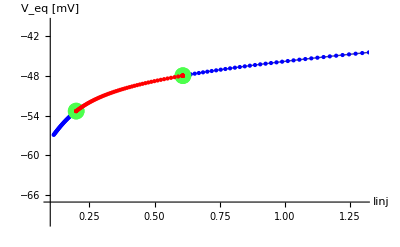

```mathematica
(*______________________________________________*)
(*______________Stability Analysis______________*)
(*______________________________________________*)
	eqType = {"As.Stable(∃λ_i: Im(λ_i)≠ 0, ∀j Re(λ_j) ∈ R^-)","CN Hopf Bif.(∀λ_j ∈ R Re(λ_j)<0, ∀λ_i ∈ C Re(λ_j)≤0, ∃h,k:λ_(h, k) = ±iω)",
				"Unstable(∃λ_i: Im(λ_i)≠ 0, ∃λ_j Re(λ_j) ∈ R^+)","As.Stable Node(∀j λ_j ∈ R^-)","Saddle(∀i λ_i ∈ R-{0},∃ λ_i ∈ R^+)",
				"CN Saddle-Node Bif.(∀i λ_i ∈ R, Re(λ_j)≤0, ∃ λ_i = 0)","BifNew( ∀j Re(λ_j)≤0, (∃h,k:λ_(h, k) = ±iω OR ∃ λ_i = 0) )",
				"Don't Care"};

zero = 10^-10;(*10^-10*)

conc0 = 0.0001;
v0 =-57;
i0 =Imin;
maxIter =10000;
deltaVV = 0.1;


eqE=Table[sys1[[iii,2]],{iii,1,dimSys}];
varList1 = Table[varEqList[[mm]]->eqE[[mm]],{mm,2,dimSys-1}];
eqE=(eqE//.varList1);

Do[
	pSol[mm] = {};
,{mm,1,dimSys}];


bif = {};
bifType = {};

maxDiv = 10;
eqCodPrec = 0;
primo = True;

sol = FindRoot[(eqE[[17]]/.{varEqList[[1]]->v0,varEqList[[17]]->concPar})==0,{concPar,conc0}];
	
	v1=v0;
	conc1=sol[[1,2]];
	i1 = FindRoot[Evaluate[(eqE[[1]]/.{varEqList[[1]]->v1,varEqList[[17]]->conc1})]==0,{Iext,Imin}][[1,2]];

	Do[
	eqPoint[mm] = {};
	eqPoint1[mm] = {};
	eigenList[mm] = {};
,{mm,1,Length[eqType]//N}];

Do[

	continua = True;

	CalcoloEqEigenBio[deltaVV];
	deltaVPrec= deltaVV;

	If[eqCodPrec≠0&&eqCodPrec != eqCod && (eqCodPrec*eqCod==3),
		nn = 1;
		While[(nn<maxDiv&& (eqCod≠2||eqCod≠7)),
			deltaVV = deltaVV/10;
			n=1;
			continua = True;
			While[(n<10&&continua),
				CalcoloEqEigenBio[deltaVV];
			n++];
		nn++];
	];

	If[eqCod==2,
		Print[eqType[[eqCod]]];
		Print["{Ieq,Veq}: ",{i2/currConvFatt,v2}];
		Print["Eigenvalues: ",eigenSingle];
    		   bif = Append[bif, {i2/currConvFatt,v2}];
		       bifType = Append[bifType, {eqType[[eqCod]],10}];
	];

	If[eqCodPrec≠0&&eqCodPrec != eqCod && (eqCodPrec*eqCod==20),
		nn = 1;
		While[(nn<maxDiv&&(eqCod≠6||eqCod≠7)) ,
			deltaVV = deltaVV/5; (*5 invece di 10*)
			n=1;
			continua = True;
			While[(n<10&&continua) ,
				CalcoloEqEigenBio[deltaVV];
			n++];
		nn++];
	];

	If[eqCod==6,
		Print[eqType[[eqCod]]];
		Print["{Ieq,Veq}: ",{i2/currConvFatt,v2}];
		Print["Eigenvalues: ",eigenSingle];
		bif = Append[bif, {i2/currConvFatt,v2}];
		       bifType = Append[bifType, {eqType[[eqCod]],10}];
	];

	If[eqCod==7,
		Print[eqType[[eqCod]]];
		Print["{Ieq,Veq}: ",{i2/currConvFatt,v2}];
		Print["Eigenvalues: ",eigenSingle];
		       bif = Append[bif, {i2/currConvFatt,v2}];
		       bifType = Append[bifType, {eqType[[eqCod]],10}];
	];

	i1=i2 ;
	v1=v2;
	    conc1=conc2;
	eqCodPrec = eqCod;
	deltaVV=deltaVPrec;

	If[(i2/currConvFatt)>Imax ||(i2/currConvFatt)<Imin, Break[];];

,{ii,1,maxIter}]; 


	Do[
		pSolTab[mm] = Table[pSol[mm][[iii]],{iii,1,Length[pSol[mm]]}];
	,{mm,1,dimSys}];

(*______________________________________________*)
(*_____________________Output___________________*)
(*______________________________________________*)


	
Needs["PlotLegends`"];

	eqCol={RGBColor[0,0,1],RGBColor[0.3,1,0.3],RGBColor[1,0,0],RGBColor[0,0.7,1],RGBColor[1,0,1],RGBColor[1,0.7,0],RGBColor[0.7,0.3,0.2],RGBColor[0,0,0]};


graph = {};
graphsLegendStyle = {};
dimSys1 = Length[eqType];

graph = Append[graph,ListLinePlot[pSolTab[1],AxesLabel->{"Iinj","V_eq [mV]"},PlotRange->{{Imin,Imax},{Vmin,Vmax}}]];

	Do[
		ll = Length[eqPoint[mm]];
		If[ll>0 && mm≠2 && mm≠6 && mm≠7,
			(*xx = Round[eqPoint[mm][[Round[(ll+1)/2]]][[1]]+dx];
			yy = Round[eqPoint[mm][[Round[(ll+1)/2]]][[2]]+dy];*)
			graph = Append[graph,
				ListPlot[eqPoint[mm],PlotStyle->{eqCol[[mm]](*,Text[eqType[[mm]],{xx,yy}]*)},AxesLabel->Automatic,Mesh->All]];
			graphsLegendStyle=Append[graphsLegendStyle,{Graphics[{eqCol[[mm]],Thick,Line[{{0,1},{1,1}}]}],Text[eqType[[mm]]]}];
		]
		If[ll>0 && (mm==2 || mm==6 || mm==7),
			Do[
			xx = Round[eqPoint[mm][[nn]][[1]]+0.10];
			yy = Round[eqPoint[mm][[nn]][[2]]-8];
				graph = Append[graph,
					ListPlot[eqPoint[mm],PlotStyle->{eqCol[[mm]],PointSize[0.03](*,Text[eqType[[mm]],{xx,yy}]*)},AxesOrigin->{0.1,-67},Mesh->All]];
			graphsLegendStyle=Append[graphsLegendStyle,{Graphics[{eqCol[[mm]],Thick,Disk[]}],Text[eqType[[mm]]]}];

			,{nn,1,ll}];
		];
		
	,{mm,1,dimSys1}];

	Print[GraphicsRow[{Show[graph,AxesOrigin->{0.1,-67}],If[Length[graphsLegendStyle]>0,Graphics[Legend[graphsLegendStyle,LegendTextSpace->10,LegendSize->{8,3}]]]}]]
```